```mathematica
morsefun[u_, v_] = ((Cos[2 Pi u]  + Cos[2 Pi v]) + 2)/4
```

1/4 (2+Cos[2 π u]+Cos[2 π v])

```mathematica
colorfn[u_, v_, t_] = If[morsefun[u, v] < t, ColorData["BlueGreenYellow"][morsefun[u, v]], Transparent]
```

If[1/4 (2+Cos[2 π u]+Cos[2 π v])<t,ColorData[BlueGreenYellow][morsefun[u,v]],Transparent]

```mathematica
Manipulate[ParametricPlot3D[{
Cos[t*(2 π)] (3+Cos[u*(2 π)]),
Sin[t*(2 π)] (3+Cos[u*(2 π)]),
Sin[u*(2 π)]
},{t,0,1},{u,0,1}, 
MeshFunctions-> {morsefun[#4, #5]&},
ColorFunction->{colorfn[#4, #5, t]&},
Mesh -> 20
], {t, 0, 1}]
```

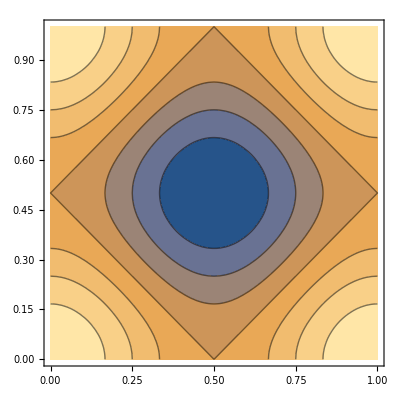

```mathematica
ContourPlot[morsefun[u, v], {u, 0, 1}, {v, 0, 1}]
```

```mathematica
ParametricPlot3D[{
Cos[t*(2 π)] (3+Cos[u*(2 π)]),
Sin[t*(2 π)] (3+Cos[u*(2 π)]),
Sin[u*(2 π)]
},{t,0,1},{u,0,1}, 
MeshFunctions-> {#2 &},
Mesh -> 20
]
```

```mathematica
ParametricPlot3D[{
Cos[t*(2 π)] (3+Cos[u*(2 π)]),
Sin[t*(2 π)] (3+Cos[u*(2 π)]),
Sin[u*(2 π)]
},{t,0,0.9},{u,0,0.9}]
```

-Graphics3D-

```mathematica
HeavisideLambda
```